```mathematica
glider=CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,1,0},{0,0,1},{1,1,1}},0},50];
```

```mathematica
deadCellDelete[list_]:=
Which[
Flatten[Position[list,1]][[1]]≠1&&Flatten[Position[list,1]][[-2]]==Length@list,
Delete[list,List/@Flatten[Range[Flatten[Position[list,1]][[1]]-1]]],

Flatten[Position[list,1]][[-2]]≠Length@list&&Flatten[Position[list,1]][[1]]==1,
Delete[list,List/@Flatten[Range[Flatten[Position[list,1]][[-2]]+1,Length@list]]],

Flatten[Position[list,1]][[1]]≠1&&Flatten[Position[list,1]][[-2]]≠Length@list,
Delete[list,List/@Flatten[Join[Range[Flatten[Position[list,1]][[1]]-1],Range[Flatten[Position[list,1]][[-2]]+1,Length@list]]]],

Flatten[Position[list,1]][[1]]==1&&Flatten[Position[list,1]][[-2]]==Length@list,
list
]
```

```mathematica
formatList[list_]:=Transpose@deadCellDelete@Transpose@deadCellDelete@list;
```

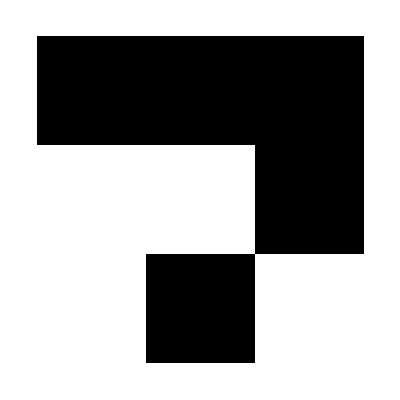

```mathematica
ArrayPlot@formatList[Reverse@glider[[1]]]
```

```mathematica
sample1=CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,0,0,0,0,0,0},{0,1,1,1,0,1,0},{0,1,0,0,0,0,0},{0,0,0,0,1,1,0},{0,0,1,1,0,1,0},{0,1,0,1,0,1,0},{0,0,0,0,0,0,0}},0},1000];
```

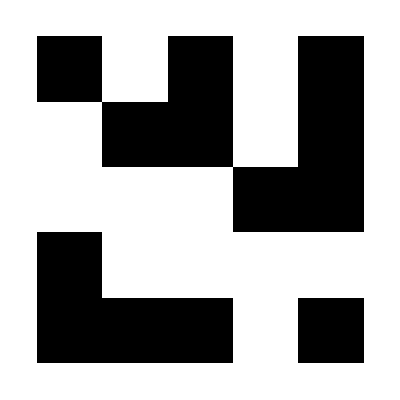

```mathematica
ArrayPlot@formatList[Reverse@sample1[[1]]]
```

```mathematica
gliderGunOriginal=CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{Transpose@{{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,1,1,0,0,0,0,0},
{0,0,0,0,1,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,1,1,1,0,0,0,0,0},
{0,0,1,0,0,0,1,0,0,0,0},
{0,1,0,0,0,0,0,1,0,0,0},
{0,1,0,0,0,0,0,1,0,0,0},
{0,0,0,0,1,0,0,0,0,0,0},
{0,0,1,0,0,0,1,0,0,0,0},
{0,0,0,1,1,1,0,0,0,0,0},
{0,0,0,0,1,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,1,1,0,0,0},
{0,0,0,0,0,1,1,1,0,0,0},
{0,0,0,0,1,0,0,0,1,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,1,1,0,0,0,1,1,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,1,1,0,0,0},
{0,0,0,0,0,0,1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0}},0},1000];
```

```mathematica
ArrayPlot@formatList[Reverse@gliderGunOriginal[[1]]]
```

-Graphics-

```mathematica
Manipulate[
ArrayPlot@glider[[var]],
{var,1,50,1}]
```

```mathematica
Manipulate[
ArrayPlot[formatList@Reverse@gliderGunOriginal[[var]]],
{var,1,1000,1}]
```

```mathematica
Manipulate[
ArrayPlot[formatList@sample1[[var]],Mesh->True],
{var,1,1000,1}]
```

```mathematica
(*Create UI for GAME*) (*Simulation*)
```

```mathematica
Module[{values},TogglerBar[Dynamic[values],Table[Module[{x=i},Row@{Invisible@x,Dynamic@If[values≠{}&&MemberQ[(values[[#,1,1,1]]==x&/@Range@Length@values),True],ArrayPlot[{{1}}],ArrayPlot[{{0}}]]}],{i,1,9,1}],Appearance->"Vertical"->{Automatic,3}]
]
```

|  | 
 |  | 
 |  |

```mathematica
Module[{placeholder={},list=CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,0,0},{0,0,0},{0,0,0}},0},50]},
Manipulate[
placeholder=values;
list=If[placeholder=={},
CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{{0,0,0},{0,0,0},{0,0,0}},0},50],CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{Transpose@Partition[ReplacePart[Flatten@{{0,0,0},{0,0,0},{0,0,0}},Thread[placeholder[[#,1,1,1]]&/@Range@Length@placeholder->Table[1,Length@placeholder]]],3],0},50]];
ArrayPlot[list[[var]]],
{{values,{},""},Table[Module[{x=i},Row@{Invisible@x,Dynamic@If[placeholder≠{}&&MemberQ[(placeholder[[#,1,1,1]]==x&/@Range@Length@placeholder),True],ArrayPlot[{{1}},ImageSize->20],ArrayPlot[{{0}},ImageSize->20]]}],{i,1,9,1}],TogglerBar,Appearance->"Vertical"->{Automatic,3}},
{var,1,Length@list,1}
]
]
```